1-1.  We see that
			Celsius=(Fahrenheit-32)*1.8.

```mathematica
Solve[x == 1.8*(x - 32), x]
```

{{x→72.}}

Thus 72 degrees is the answer.

1-4. (1).

```mathematica
Voltage[t_]:=0.21*t-1.0*10^-4*t^2      (*Where Voltage's unit is mV*)
```

```mathematica
Map[Voltage,{-100,200,400,500}]
```

{-22.,38.,68.,80.}

```mathematica
Transpose[{{-100,200,400,500},{-22.,38.,68.,80.}}]
```

{{-100,-22.},{200,38.},{400,68.},{500,80.}}

```mathematica
TableForm[%,TableHeadings->{None,{"Temperature/^oC","Voltage/mV"}}]
```

Temperature/^oC | Voltage/mV
-100 | -22.
200 | 38.
400 | 68.
500 | 80.

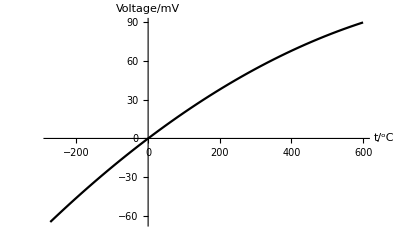

```mathematica
Plot[Voltage[t],{t,-273.15,600},AxesLabel->{"t/^oC","Voltage/mV"},PlotStyle->Black]
```

#### (2).

```mathematica
Solve[a*Voltage[0]+b==0&&a*Voltage[100]==100,{a,b}]
```

{{a→5.,b→0.}}

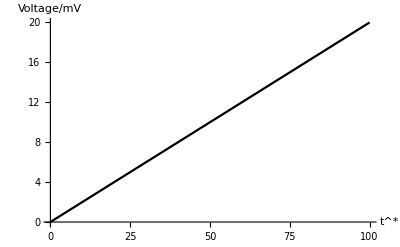

```mathematica
Plot[1/5 t,{t,0,100},AxesLabel->{"t^*","Voltage/mV"},PlotStyle->Black]
```

#### (3).

```mathematica
Map[Voltage,{-100,200,400,500}];
TableForm[Transpose[{5*%,{-100,200,400,500}}],TableHeadings->{None,{"t^*/^o","t/^oC"}}]
```

t^*/^o | t/^oC
-110. | -100
190. | 200
340. | 400
400. | 500

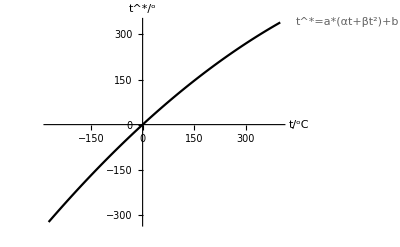

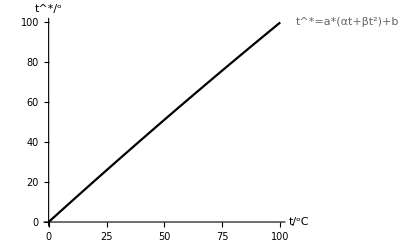

```mathematica
Plot[5*Voltage[t],{t,-273.15,400},PlotLabels->"t^*=a*(αt+βt^2)+b",AxesLabel->{"t/^oC","t^*/^o"},PlotStyle->Black]
Plot[5*Voltage[t],{t,0,100},PlotLabels->"t^*=a*(αt+βt^2)+b",AxesLabel->{"t/^oC","t^*/^o"},PlotStyle->Black]
```

#### (4).

We can see from the graph above that t^* and t(^o C) share identical behavior between 0~100 ^oC. However, they begin to differ in the lower or higher temperature.

#### 1-12.

```mathematica
1/4*Pi*d^2/.d->1.1*10^-3
```

9.50332×10^-7

```mathematica
Solve[p+h*ρ*g==(p*Subscript[V, R])/(S*h),p]/.{h->23*10^-3,S->%,ρ->13.6*10^3,Subscript[V, R]->130*10^-6,g->9.80}
```

{{p→0.515496}}

```mathematica
(p/.%)/(13.6*10^3*9.8)
```

{3.86777×10^-6}

Which means the pressure is 0.515 Pa, or 3.87×10^-3mmHg.

#### Exercise 1 - 4.

```mathematica
Integrate[x^3*1/(2Pi*σ)^2*Exp[(-(x-μ)^2)/(2 σ^2)],x]
```

(ⅇ^(-(x^2+μ^2)/(2 σ^2)) (-2 ⅇ^((x μ)/σ^2) σ (x^2+x μ+μ^2+2 σ^2)+ⅇ^((x^2+μ^2)/(2 σ^2)) √(2 π) μ (μ^2+3 σ^2) Erf[(x-μ)/(√2 σ)]))/(8 π^2 σ)

Where Erf(z)=2/(√π)∫_0^z e^(-t^2)dt.

```mathematica
Integrate[x^4*1/(2Pi*σ)^2*Exp[(-(x-μ)^2)/(2 σ^2)],x]
```

(ⅇ^(-(x^2+μ^2)/(2 σ^2)) (-2 ⅇ^((x μ)/σ^2) σ (x^3+x^2 μ+μ^3+5 μ σ^2+x (μ^2+3 σ^2))+ⅇ^((x^2+μ^2)/(2 σ^2)) √(2 π) (μ^4+6 μ^2 σ^2+3 σ^4) Erf[(x-μ)/(√2 σ)]))/(8 π^2 σ)

#### Exercise 1 - 5.

P=(n!)/(∏_(i=1)^m n_i!)

#### 1-15.

ρ_mass=(0.76*28+0.23*32+0.01*40)/1=29.04 g/mol

ρ=ρ_mass/(22.4*10^-3)=(29.04*10^-3)/(22.4*10^-3)=1.30 kg/m^3

```mathematica
Exercise 1-7.
```

#### (a) van der Waals Equation: (p+(a n^2)/V^2)(V-n b)=n R T

The critical point satisfies  ((∂P)/(∂V))_T=0, ((∂^2 P)/(∂V^2))_(T=T_C)=0.

```mathematica
Reduce[D[(R*T)/(V-b)-a/V^2,V]==0,T]
```

(R==0&&a==0&&b V-V^2≠0)||(R V≠0&&T==(2 a (b-V)^2)/(R V^3)&&b-V≠0)

```mathematica
Reduce[D[D[(R*T)/(V-b)-a/V^2,V],V]==0,T]
```

(R==0&&a==0&&b V-V^2≠0)||(R V≠0&&T==-(3 a (b-V)^3)/(R V^4)&&b-V≠0)

```mathematica
Solve[-(3 a (b-V)^3)/(R V^4)==(2 a (b-V)^2)/(R V^3),V]
```

{{V→b},{V→b},{V→3 b}}

```mathematica
(2 a (b-V)^2)/(R V^3)/.V->3b
```

(8 a)/(27 b R)

```mathematica
(R*T)/(V-b)-a/V^2/.{V->3b,T->%}
```

a/(27 b^2)

Thus p_c = a/(27 b^2), V_c = 3b, T_c = (8a)/(27 b R).

#### (b). (c). (It seems the answers have been mixed up, due to the codes)

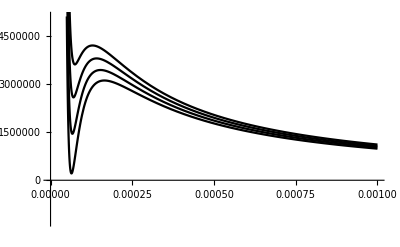

```mathematica
p[V_]:=(R*T)/(V-b)-a/V^2/.{a->0.1378,b->3.183*10^-5,R->8.314};
T=Range[131,150,5];
plot[x_]:=Plot[x,{V,0,0.001},PlotStyle->Black];
Show@@Map[plot,p[V]]
Clear[T];
```

```mathematica
Clear[T,T0,p0];
Judgep[p_,T_]:=Module[{function,valuep,pressure,Vroot},
		pressure[V_]:=(R*T)/(V-b)-a/V^2/.{a->0.1378,b->3.183*10^-5,R->8.314};
		Vroot[x_]:=Sort[Flatten[NSolve[pressure[V]==x,V]]];
		function=Integrate[p-pressure[V],V];
		valuep[x_]:=(function/.Vroot[x][[3]])-(function/.Vroot[x][[1]]);
		valuep[p]
];
Result={};
For[T=131,T<151,T=T+0.1,
list1=Table[{p,T},{p,1*10^6,5*10^6,10000}];
list2=Map[Abs,Map[Judgep@@#&,list1]];
list3=SortBy[Transpose[{list1,list2}],Last];
Result=AppendTo[Result,First[list3]];
];
(*The raw data is hidden - click the blancket on the right to see it*)
Result=Flatten[Drop[#,-1]&/@Result,1];
```

{{{2530000,131},0.242736},{{2540000,131.1},0.591113},{{2550000,131.2},0.931394},{{2550000,131.3},1.17615},{{2560000,131.4},0.837614},{{2570000,131.5},0.506992},{{2580000,131.6},0.184185},{{2590000,131.7},0.130901},{{2600000,131.8},0.438361},{{2610000,131.9},0.738285},{{2620000,132.},1.03076},{{2620000,132.1},1.03252},{{2630000,132.2},0.741189},{{2640000,132.3},0.457133},{{2650000,132.4},0.180259},{{2660000,132.5},0.0895189},{{2670000,132.6},0.352287},{{2680000,132.7},0.608131},{{2690000,132.8},0.857136},{{2700000,132.9},1.09938},{{2700000,133.},0.913787},{{2710000,133.1},0.672057},{{2720000,133.2},0.436924},{{2730000,133.3},0.208307},{{2740000,133.4},0.0138747},{{2750000,133.5},0.2297},{{2760000,133.6},0.439247},{{2770000,133.7},0.642594},{{2780000,133.8},0.839818},{{2790000,133.9},1.03099},{{2790000,134.},0.926283},{{2800000,134.1},0.734965},{{2810000,134.2},0.549548},{{2820000,134.3},0.369958},{{2830000,134.4},0.196123},{{2840000,134.5},0.0279687},{{2850000,134.6},0.134576},{{2860000,134.7},0.291581},{{2870000,134.8},0.443119},{{2880000,134.9},0.589258},{{2890000,135.},0.730067},{{2900000,135.1},0.865615},{{2910000,135.2},0.99597},{{2910000,135.3},0.887496},{{2920000,135.4},0.756194},{{2930000,135.5},0.629953},{{2940000,135.6},0.508709},{{2950000,135.7},0.392396},{{2960000,135.8},0.280948},{{2970000,135.9},0.174303},{{2980000,136.},0.0723955},{{2990000,136.1},0.0248366},{{3000000,136.2},0.117456},{{3010000,136.3},0.205524},{{3020000,136.4},0.289103},{{3030000,136.5},0.368254},{{3040000,136.6},0.443036},{{3050000,136.7},0.51351},{{3060000,136.8},0.579734},{{3070000,136.9},0.641768},{{3080000,137.},0.69967},{{3090000,137.1},0.753498},{{3100000,137.2},0.803308},{{3110000,137.3},0.849159},{{3120000,137.4},0.891106},{{3120000,137.5},0.864427},{{3130000,137.6},0.820276},{{3140000,137.7},0.779917},{{3150000,137.8},0.743294},{{3160000,137.9},0.710354},{{3170000,138.},0.68104},{{3180000,138.1},0.655301},{{3190000,138.2},0.633081},{{3200000,138.3},0.614328},{{3210000,138.4},0.598989},{{3220000,138.5},0.587012},{{3230000,138.6},0.578345},{{3240000,138.7},0.572935},{{3250000,138.8},0.570733},{{3260000,138.9},0.571687},{{3270000,139.},0.575746},{{3280000,139.1},0.582861},{{3290000,139.2},0.592981},{{3300000,139.3},0.606057},{{3310000,139.4},0.62204},{{3320000,139.5},0.640881},{{3330000,139.6},0.662531},{{3340000,139.7},0.686943},{{3350000,139.8},0.714068},{{3360000,139.9},0.743858},{{3370000,140.},0.776267},{{3390000,140.1},0.742828},{{3400000,140.2},0.696731},{{3410000,140.3},0.648199},{{3420000,140.4},0.597276},{{3430000,140.5},0.544009},{{3440000,140.6},0.488442},{{3450000,140.7},0.43062},{{3460000,140.8},0.370589},{{3470000,140.9},0.308393},{{3480000,141.},0.244077},{{3490000,141.1},0.177684},{{3500000,141.2},0.109259},{{3510000,141.3},0.0388453},{{3520000,141.4},0.0335136},{{3530000,141.5},0.107774},{{3540000,141.6},0.183893},{{3550000,141.7},0.261828},{{3560000,141.8},0.341535},{{3570000,141.9},0.422972},{{3580000,142.},0.506097},{{3590000,142.1},0.590866},{{3600000,142.2},0.677239},{{3620000,142.3},0.595705},{{3630000,142.4},0.498513},{{3640000,142.5},0.399876},{{3650000,142.6},0.299835},{{3660000,142.7},0.198432},{{3670000,142.8},0.0957075},{{3680000,142.9},0.0082973},{{3690000,143.},0.113542},{{3700000,143.1},0.219985},{{3710000,143.2},0.327585},{{3720000,143.3},0.436304},{{3730000,143.4},0.546098},{{3750000,143.5},0.600283},{{3760000,143.6},0.481107},{{3770000,143.7},0.361003},{{3780000,143.8},0.240011},{{3790000,143.9},0.118171},{{3800000,144.},0.00447678},{{3810000,144.1},0.127893},{{3820000,144.2},0.252037},{{3830000,144.3},0.376868},{{3840000,144.4},0.502348},{{3860000,144.5},0.543829},{{3870000,144.6},0.410106},{{3880000,144.7},0.275879},{{3890000,144.8},0.141186},{{3900000,144.9},0.00606906},{{3910000,145.},0.129433},{{3920000,145.1},0.26528},{{3930000,145.2},0.401432},{{3940000,145.3},0.537849},{{3960000,145.4},0.422451},{{3970000,145.5},0.278777},{{3980000,145.6},0.134978},{{3990000,145.7},0.00890366},{{4000000,145.8},0.152829},{{4010000,145.9},0.296756},{{4020000,146.},0.440644},{{4040000,146.1},0.452447},{{4050000,146.2},0.302058},{{4060000,146.3},0.151847},{{4070000,146.4},0.00185602},{{4080000,146.5},0.147873},{{4090000,146.6},0.297298},{{4100000,146.7},0.446376},{{4120000,146.8},0.382754},{{4130000,146.9},0.227916},{{4140000,147.},0.0735643},{{4150000,147.1},0.0802569},{{4160000,147.2},0.233504},{{4170000,147.3},0.386132},{{4190000,147.4},0.387881},{{4200000,147.5},0.230128},{{4210000,147.6},0.0731363},{{4220000,147.7},0.0830481},{{4230000,147.8},0.238379},{{4240000,147.9},0.392808},{{4260000,148.},0.32821},{{4270000,148.1},0.169289},{{4280000,148.2},0.0114152},{{4290000,148.3},0.145361},{{4300000,148.4},0.300989}}

```mathematica
lista=Table[{i,Range[1*10^6,5*10^6,10000]},{i,130,150,0.1}];
function[t_,x_List]:=First[SortBy[{t,#,Abs[Judgep[#,t]]}&/@x,Last]];   
listb=Map[function@@#&,lista]
(*codes that are more Mathematica-like*)
```

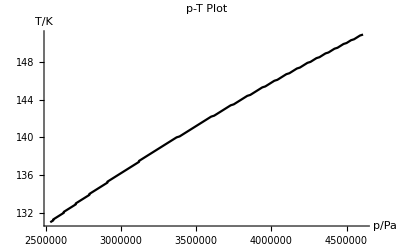

```mathematica
ListLinePlot[Result,AxesLabel->{"p/Pa","T/K"},PlotLabel->"p-T Plot",PlotStyle->Black]
```

419506.-1.22725 x+1.60702×10^-6 x^2-1.24004×10^-12 x^3+6.24465×10^-19 x^4-2.14456×10^-25 x^5+5.08679×10^-32 x^6-8.22937×10^-39 x^7+8.69098×10^-46 x^8-5.41103×10^-53 x^9+1.50835×10^-60 x^10

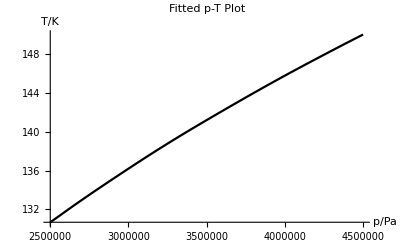

```mathematica
Fit[Result,Table[x^i,{i,0,10}],x]
Plot[%,{x,2.5*10^6,4.5*10^6},AxesLabel->{"p/Pa","T/K"},PlotLabel->"Fitted p-T Plot",PlotStyle->Black]
```

#### The answer of (c):

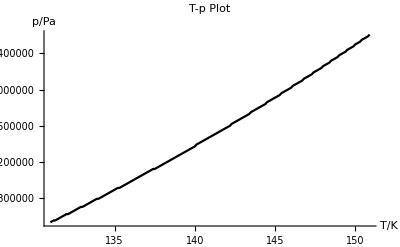

1.32635×10^13-5.78415×10^11 x+9.59629×10^9 x^2-6.34996×10^7 x^3-78715. x^4+3131.55 x^5-5.07783 x^6-0.142634 x^7+0.00108987 x^8-3.25204×10^-6 x^9+3.673×10^-9 x^10

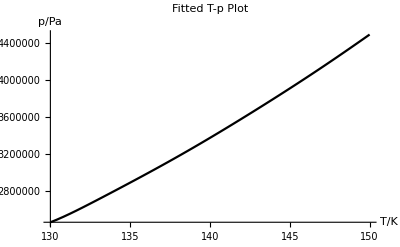

```mathematica
change[{a_,b_}]:={b,a};
result=change/@Result;
ListLinePlot[result,AxesLabel->{"T/K","p/Pa"},PlotLabel->"T-p Plot",PlotStyle->Black]
Fit[result,Table[x^i,{i,0,10}],x]
Plot[%,{x,130,150},AxesLabel->{"T/K","p/Pa"},PlotLabel->"Fitted T-p Plot",PlotStyle->Black]
```

#### The answer of (b):

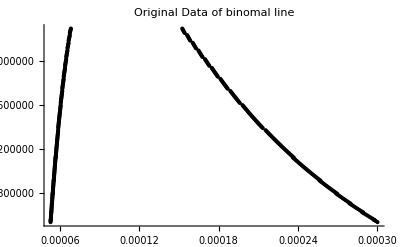

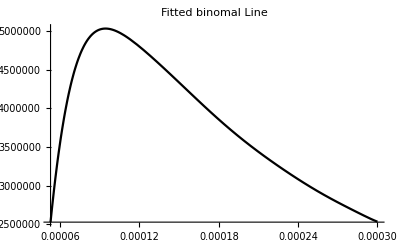

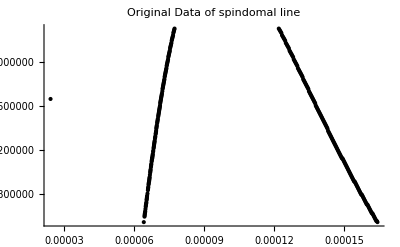

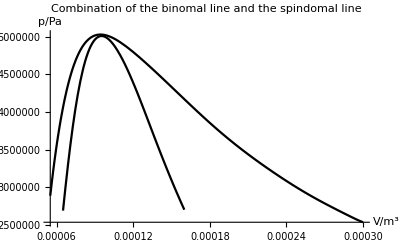

```mathematica
GetV1[p_,T_]:=V/.Sort[NSolve[((p+a/V^2)*(V-b)==R*T/.{a->0.1378,b->3.183*10^-5,R->8.314}),V]];
list1={#,GetV1@@#}&/@Result;
manipulation[{{p_,T_},{v1_,v2_,v3_}}]:={{v1,p},{v3,p}};
list2=Flatten[manipulation/@list1,1];
ListPlot[list2,PlotRange->All,PlotLabel->"Original Data of binomal line",PlotStyle->Black]
linea=Fit[list2,Table[x^i,{i,0,10}],x];
Plot[linea,{x,0.00005276501246197953,0.00030},PlotRange->All,PlotLabel->"Fitted binomal Line",PlotStyle->Black]
(*codes above are to get the binomal line, below are to get the spindomal line*)
GetV2[p_,T_]:=V/.Sort[NSolve[(2 a)/V^3-(R T)/(-b+V)^2==0/.{a->0.1378,b->3.183/10^5,R->8.314},V]];
lista={#,GetV2@@#}&/@Result;
manipulate[{p_,T_},{v__}]:={#,p}&/@{v};
listb=Drop[Flatten[(manipulate@@#)&/@lista,1],1];
ListPlot[listb,PlotRange->All,PlotLabel->"Original Data of spindomal line",PlotStyle->Black]
lineb=Fit[listb,Table[x^i,{i,0,10}],x];
Show[Plot[linea,{x,0.000055,0.00030},PlotRange->All,PlotStyle->Black],
Plot[lineb,{x,0.000065,0.00016},PlotRange->All,PlotStyle->Black],
PlotLabel->"Combination of the binomal line and the spindomal line",AxesLabel->{"V/m^3","p/Pa"}]
```

#### 8.

```mathematica
D[(p+(a*n^2)/V^2)*(V-n*b),V]
```

p+(a n^2)/V^2-(2 a n^2 (-b n+V))/V^3

Which means n R ((∂T)/(∂V))_p=p+(a n^2)/V^2-(2 a n^2 (-b n+V))/V^3
Thus ((∂T)/(∂V))_p=(n R)/(p+(a n^2)/V^2-(2 a n^2 (-b n+V))/V^3)  .
The volume expansion coefficient α = (((∂T)/(∂V))_p)/V=(n R)/(V p+(a n^2)/V-(2 a n^2 (-b n+V))/V^2) .

```mathematica
D[(p+(a*n^2)/V^2)*(V-n*b),p]
```

-b n+V

Which means n R ((∂T)/(∂p))_V=V-n b
Thus ((∂p)/(∂T))_V=(n R)/(V- n b)  .
The pressure coefficient β = (((∂p)/(∂T))_V)/p=(n R)/(p(V -n b)) .

```mathematica
Reduce[(p+(a*n^2)/V^2)*(V-n*b)==n*R*T,p]
```

((b n-V) V≠0&&p==(-a b n^3+a n^2 V-n R T V^2)/((b n-V) V^2))||(T==0&&n≠0&&b==V/n&&V≠0)||(T≠0&&R==0&&n≠0&&b==V/n&&V≠0)

```mathematica
D[(-a b n^3+a n^2 V-n R T V^2)/((b n-V) V^2),V]
```

(a n^2-2 n R T V)/((b n-V) V^2)-(2 (-a b n^3+a n^2 V-n R T V^2))/((b n-V) V^3)+(-a b n^3+a n^2 V-n R T V^2)/((b n-V)^2 V^2)

```mathematica
FullSimplify[%5]
```

n ((2 a n)/V^3-(R T)/(-b n+V)^2)

```mathematica
FullSimplify[1/%]
```

1/(n ((2 a n)/V^3-(R T)/(-b n+V)^2))

Which means ((∂p)/(∂V))_T=n ((2 a n)/V^3-(R T)/(-b n+V)^2).
Thus ((∂V)/(∂p))_T=1/(n ((2 a n)/V^3-(R T)/(-b n+V)^2))  .
The isothermal compressibility coefficient κ = -(((∂V)/(∂p))_T)/V=-1/(n V((2 a n)/V^3-(R T)/(-b n+V)^2)) .

Assume that there is 1 mol of O_2.

```mathematica
Drop[NSolve[((p+a/V^2)*(V-b)==R*T/.{a->0.1378,b->3.183*10^-5,R->8.314,T->300,p->1*10^5}),V],-2]
```

{{V→0.0249186}}

```mathematica
Flatten[%]
```

{V→0.0249186}

```mathematica
(p+(a n^2)/V^2-(2 a n^2 (-b n+V))/V^3)/V/.{a->0.1378,b->3.183*10^-5,R->8.314,T->300,p->1*10^5,n->1,V->0.02491860058233183}
```

4.00418×10^6

```mathematica
(n*R)/(p*(V-n*b))/.{a->0.1378,b->3.183*10^-5,R->8.314,T->300,p->1*10^5,n->1,V->0.02491860058233183}
```

0.00334073

```mathematica
1/(n*V* ((2 a n)/V^3-(R T)/(-b n+V)^2))/.{a->0.1378,b->3.183*10^-5,R->8.314,T->300,p->1*10^5,n->1,V->0.02491860058233183}
```

-0.0000100094

Thus α=4.004*10^6, β= 3.341*10^-3, κ=1.001*10^-5. (All in SI Units)

```mathematica
GetV2
```

GetV2

```mathematica
?GetV2
```

Global`GetV2

GetV2[p_,T_]:=V/.Sort[NSolve[(2 a)/V^3-(R T)/(-b+V)^2==0/.{a→0.1378,b→3.183/10^5,R→8.314},V]]

```mathematica
{{{{GetV2[p_,T_]:=V/.Sort[NSolve[(2 a)/V^3-(R T)/(-b+V)^2==0/.{a->0.1378,b->3.183/10^5,R->8.314},V]]}}}}
```

```mathematica
lista
```

{{0.000164679},{0.0000641166,0.000164438},{0.000164196},{0.000163955},{0.000163714},{0.000163474},{0.000163233},{0.0000644216,0.000162992},{0.000064473,0.000162752},{0.0000645245,0.000162512},{0.0000645763,0.000162272},{0.000162031},{0.0000646802,0.000161792},{0.0000647325,0.000161552},{0.000161312},{0.0000648375,0.000161072},{0.000160833},{0.0000649433,0.000160593},{0.0000649964,0.000160354},{0.0000650497,0.000160115},{0.000159876},{0.0000651569,0.000159637},{0.0000652108,0.000159398},{0.000159159},{0.0000653191,0.00015892},{0.0000653736,0.000158682},{0.0000654282,0.000158443},{0.0000654831,0.000158205},{0.0000655381,0.000157966},{0.000157728},{0.00015749},{0.0000657044,0.000157252},{0.000157013},{0.000156775},{0.0000658724,0.000156537},{0.0000659289,0.0001563},{0.0000659855,0.000156062},{0.0000660424,0.000155824},{0.000155586},{0.0000661567,0.000155349},{0.0000662142,0.000155111},{0.0000662719,0.000154873},{0.000154636},{0.000066388,0.000154398},{0.0000664464,0.000154161},{0.000066505,0.000153924},{0.0000665638,0.000153686},{0.0000666229,0.000153449},{0.000153212},{0.0000667417,0.000152975},{0.000152737},{0.0000668615,0.0001525},{0.0000669217,0.000152263},{0.0000669822,0.000152026},{0.0000670429,0.000151789},{0.000151552},{0.0000671651,0.000151314},{0.0000672265,0.000151077},{0.0000672883,0.00015084},{0.0000673502,0.000150603},{0.000150366},{0.0000674749,0.000150129},{0.0000675377,0.000149892},{0.0000676007,0.000149655},{0.000067664,0.000149418},{0.0000677275,0.000149181},{0.0000677914,0.000148944},{0.0000678555,0.000148706},{0.0000679199,0.000148469},{0.0000679845,0.000148232},{0.000147995},{0.0000681147,0.000147757},{0.0000681802,0.00014752},{0.000147283},{0.0000683121,0.000147045},{0.0000683785,0.000146808},{0.0000684452,0.00014657},{0.0000685123,0.000146333},{0.0000685796,0.000146095},{0.0000686472,0.000145857},{0.0000687151,0.00014562},{0.0000687834,0.000145382},{0.000145144},{0.0000689209,0.000144906},{0.0000689901,0.000144668},{0.0000690597,0.00014443},{0.000144191},{0.0000691998,0.000143953},{0.0000692704,0.000143715},{0.0000693414,0.000143476},{0.0000694126,0.000143237},{0.0000694843,0.000142999},{0.0000695563,0.00014276},{0.0000696286,0.000142521},{0.0000697013,0.000142282},{0.000142042},{0.0000698479,0.000141803},{0.0000699217,0.000141563},{0.000069996,0.000141324},{0.0000700706,0.000141084},{0.0000701456,0.000140844},{0.000140603},{0.0000702968,0.000140363},{0.000070373,0.000140123},{0.0000704497,0.000139882},{0.0000705267,0.000139641},{0.0000706042,0.0001394},{0.0000706821,0.000139159},{0.0000707604,0.000138917},{0.0000708392,0.000138676},{0.0000709184,0.000138434},{0.0000709981,0.000138192},{0.0000710782,0.000137949},{0.0000711588,0.000137707},{0.0000712399,0.000137464},{0.0000713215,0.000137221},{0.0000714035,0.000136977},{0.0000240781,0.000071486,0.000136734},{0.000071569,0.00013649},{0.0000716525,0.000136246},{0.0000717365,0.000136001},{0.0000718211,0.000135757},{0.0000719061,0.000135512},{0.000135266},{0.0000720779,0.000135021},{0.0000721645,0.000134775},{0.0000722518,0.000134529},{0.0000723396,0.000134282},{0.000072428,0.000134035},{0.0000725169,0.000133788},{0.0000726065,0.00013354},{0.0000726966,0.000133292},{0.0000727874,0.000133043},{0.0000728788,0.000132794},{0.0000729708,0.000132545},{0.0000730634,0.000132296},{0.0000731567,0.000132045},{0.0000732506,0.000131795},{0.0000733453,0.000131544},{0.0000734406,0.000131292},{0.0000735366,0.00013104},{0.0000736333,0.000130788},{0.0000737307,0.000130535},{0.0000738288,0.000130282},{0.0000739277,0.000130028},{0.0000740274,0.000129773},{0.0000741278,0.000129518},{0.000074229,0.000129262},{0.000074331,0.000129006},{0.0000744338,0.000128749},{0.0000745374,0.000128492},{0.0000746419,0.000128234},{0.0000747473,0.000127975},{0.0000748535,0.000127715},{0.0000749606,0.000127455},{0.0000750686,0.000127195},{0.0000751776,0.000126933},{0.0000752875,0.000126671},{0.0000753984,0.000126408},{0.0000755103,0.000126144},{0.0000756232,0.000125879},{0.0000757371,0.000125614},{0.0000758521,0.000125348},{0.0000759681,0.00012508},{0.0000760853,0.000124812},{0.0000762036,0.000124543},{0.000076323,0.000124274},{0.0000764437,0.000124003},{0.0000765655,0.000123731},{0.0000766886,0.000123458},{0.0000768129,0.000123184},{0.0000769386,0.000122909},{0.0000770656,0.000122632},{0.000077194,0.000122355},{0.0000773237,0.000122076}}